Autor: Krzysztof Dragon

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 8

Metoda różnic skończonych

Nieustalony przepływ ciepła (schemat jawny)

Napisać procedurę realizującą schemat jawny metody różnic skończonych dla zagadnienia nieustalonego przepływu ciepła:

c ρ (∂u)/(∂t)=λ (∂^2 u)/(∂x^2),   x∈(a,b),  t∈(0,t^*),

z warunkiem początkowym:

u(x,0) = u_0(x),

oraz warunkami brzegowymi pierwszego rodzaju:

u(a,t)=u_a(t),
u(b,t)=u_b(t).

Jako argument procedury należy podać liczbę nx węzłów siatki oraz czas końca t^*, natomiast krok czasu dt należy wyznaczyć (w programie) tak aby zapewnić stabilność obliczeń.

a) Korzystając z napisanej procedury wyznaczyć rozwiązanie przybliżone zagadnienia, w którym:

a=1, b=2,  t^*=1, 
c=1,  ρ=1, λ=1,

u_0(x)=x^3/6,
u_a(t)=t+1/6,
u_b(t)=2t+4/3.

Przedział [a,b] podzielić na 10 części.

Na wspólnym rysunku wykreślić rozwiązanie dokładne, którym jest funkcja u(x,t)=x^3/6+x t, oraz uzyskane rozwiązania przybliżone w chwili końcowej. Wykreślić także błędy uzyskanego rozwiązania przybliżonego w chwili końcowej.

## Rozwiązanie

```mathematica
Clear[npc1rsj];
npc1rsj[u0_,ua_,ub_,a_,b_,nx_,tk_,c_,ρ_,λ_]:= Module[{dx,dt,nt,x,t,u,u1,r,i,k,wynik},
dx = (b-a)/nx;
dt=(c*ρ)/(2*λ) * (dx)^2;
(* Print[dt]; *)
nt = Floor[tk/dt]+1;
x = Table[a+i*dx,{i,0,nx}];
t=Table[0+k*dt,{k,0,nt}];
u=Table[u0[x_[[i]]],{i,1,nx+1}];
u1 = u;

r=λ/(c*ρ)* dt/(dx)^2;

Do[
Do[u1_[[i]]=r*u_[[i-1]]+(1-2*r)*u_[[i]]+r*u_[[i+1]],{i,2,nx}];
u1_[[1]]=ua[t_[[k]]];
u1_[[nx+1]]=ub[t_[[k]]];
u = u1, {k,2,nt+1}];
wynik = Transpose[{x,u}];
Return[wynik]
]
```

```mathematica
(* Zadanie - podzielić przedział na 10 części*)
```

```mathematica
a = 1.;
b = 2;
tk = 1;
c = 1;
ρ = 1;
λ = 1;
nx = 10;

u0[x_] := (x^3)/6;
ua[t_] := t+ 1/6;
ub[t_] := 2t+4/3;

rozwdokladne[x_] := ((x^3)/6) + x*tk;
```

```mathematica
przyblizone = npc1rsj[u0,ua,ub,a,b,nx,tk,c,ρ,λ]
```

{{1.,1.16667},{1.1,1.32183},{1.2,1.488},{1.3,1.66617},{1.4,1.85733},{1.5,2.0625},{1.6,2.28267},{1.7,2.51883},{1.8,2.772},{1.9,3.04317},{2.,3.33333}}

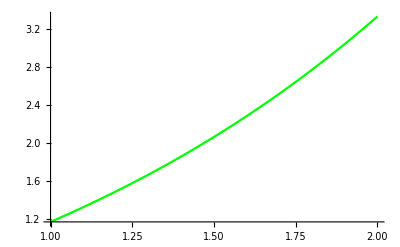

```mathematica
plt1=Plot[rozwdokladne[x],{x,a,b}, PlotStyle->{Green, PointSize[0.01]}]
plt2 = ListPlot[przyblizone, PlotStyle->{Red, PointSize[0.01]},PlotRange -> All];
```

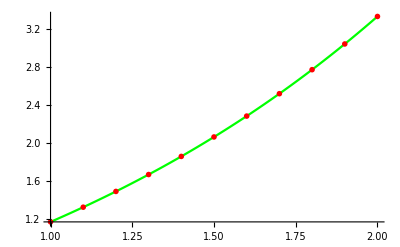

```mathematica
Show[plt1,plt2]
```

```mathematica
(* Błędy *)
```

```mathematica
krok = (b-a)/nx;
ydok= Table[rozwdokladne[x],{x,a,b,krok}];
bledy= Table [{przyblizone[[j,1]], Abs[przyblizone[[j,2]] - ydok[[j]]]},{j,1,Length[przyblizone]}]
```

{{1.,2.22045×10^-16},{1.1,2.22045×10^-16},{1.2,4.44089×10^-16},{1.3,2.22045×10^-16},{1.4,8.88178×10^-16},{1.5,8.88178×10^-16},{1.6,8.88178×10^-16},{1.7,4.44089×10^-16},{1.8,0.},{1.9,8.88178×10^-16},{2.,8.88178×10^-16}}

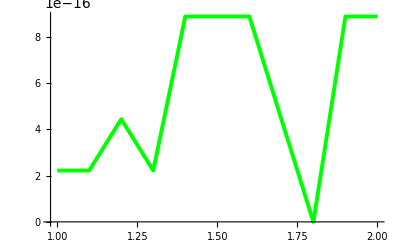

```mathematica
wb = ListPlot[bledy, Joined->True, PlotStyle->{Green, Thickness -> 0.007},PlotRange->All]
```